# Project 2: Integration with Mathematica

Names:
• Leigh Cox
• Kristina Ilyovska
• Thu Luu
• Bob Schmitz

#### Instructions:

This is due Tuesday, 11/6, at 11:59pm.
Email me a Mathematica notebook with your completed project by the due date.
You may work in groups of up to 4 students. It’s ok to divide up the work, but in the end, EVERYONE should understand the solutions to ALL the problems (not just each person does one then you paste them all together).

## Introduction and Examples

In the last few versions, Mathematica’s integration features have grown a lot. Combined with its ability to plot regions in 2D and 3D, it is a powerful tool for computing integrals. 
The primary commands used in this assignment will be the following:

Integrate[ ]  - to compute the integral of a function. It is used for double and triple integrals, as well as iterated integrals.
ImplicitRegion[ ] - to define a region in ℝ^n. The regions are defined by inequalities, often connect by && (and). 
RegionPlot[ ] and RegionPlot3D[ ] - to plot the region of integration. 

Here are some examples of the syntax:
Suppose we want to find the area of the top half of the unit disc, which we will call r, using a double integral. We integrate the function f[x,y] = 1 over r. Here’s some code we could use:

ImplicitRegion[x^2+y^2≤1&&y≥0,{x,y}]

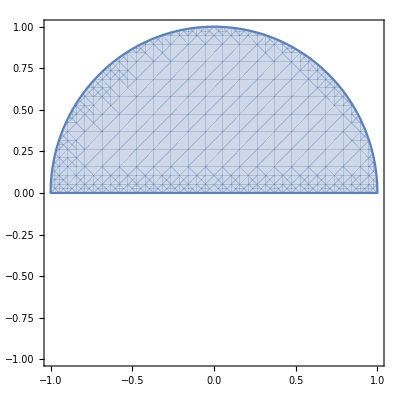

π/2

π/2

```mathematica
r = ImplicitRegion[x^2 + y^2 ≤ 1 && y≥ 0,{x,y}] (* Defines the region and calls it r. && is used to connect two inequalities. You always put a list with the variables as the second argument. *)

RegionPlot[x^2 + y^2 ≤ 1 && y≥ 0, {x,-1,1},{y,-1,1}] 
(* Putting the inequalities directly in RegionPlot[ ] lets you specify more about the plot, and in RegionPlot3D, allows you to control the Mesh as well. *)

Integrate[1,{x,y}∈r] 
(* This gives the double integral of f(x,y) = 1 over the region r. The symbol ∈ means "is an element of", and can be found on the palette or with the command Esc el Esc. *)

Integrate[1,{x,-1,1},{y,0,Sqrt[1-x^2]}] 
(* This is the iterated integral. Note that the order is a little backwards. It does the y integral first, but you put the y limits last. *)
```

Note that you can also use ContourPlot[ ] (or ContourPlot3D[ ]) to plot the boundary of the region, but you have to infer the shading yourself. This does let you distinguish between different parts of the boundary, though. We plot the equations for the boundary in a list { }, using double equals signs:

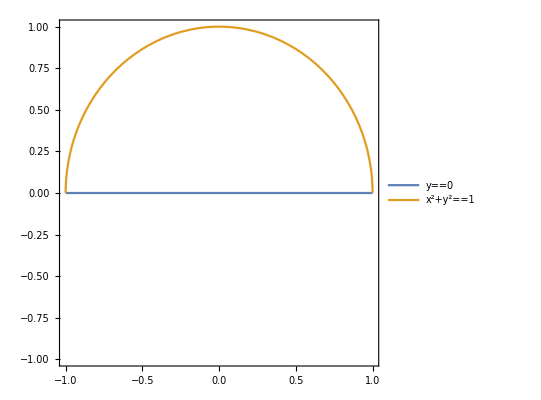

```mathematica
ContourPlot[{y==0,x^2+y^2==1},{x,-1,1},{y,-1,1},RegionFunction->(#2≥ 0&),PlotLegends->"Expressions"]
```

If you really need to, you can Show[ ] these together:

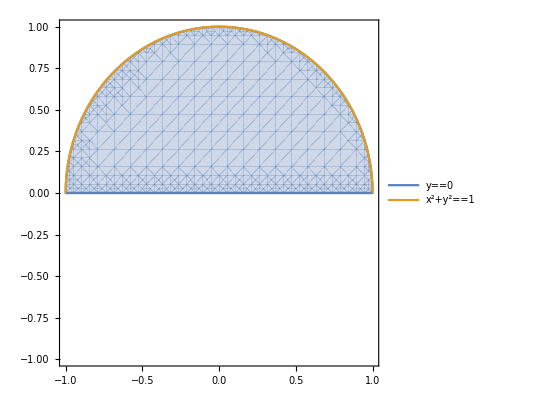

```mathematica
Show[
RegionPlot[x^2 + y^2 ≤ 1 && y≥ 0, {x,-1,1},{y,-1,1}] ,
ContourPlot[{y==0,x^2+y^2==1},{x,-1,1},{y,-1,1},RegionFunction->(#2≥ 0&),PlotLegends->"Expressions"]
]
```

For double integrals, you can also use 3DPlot[ ] together with the RegionFunction option, but there’s no 4DPlot[ ] for triple integrals, and this picture isn’t so useful anyways.

```mathematica
Plot3D[1,{x,-1,1},{y,-1,1},RegionFunction->(#1^2 + #2^2 ≤ 1 && #2 ≥ 0 &),Filling->Axis]
```

-Graphics3D-

## Problem 1: A Double Integral

Consider the iterated integral:

∫_0^3 ∫_(x^2)^9 x √y ⅆyⅆx

1) Use Mathematica to plot the region of integration, then to compute the value of the integral in three ways:
	a) As an iterated integral with the order of integration as above.
	b) As a double integral over the region of integration.
	c) As an iterated integral with the order of integration reversed. 

2) Use Plot3D[ ] with a RegionFunction and the options Filling-> Axis and PlotRange->All option to sketch the 3D region you are finding the volume of.

Hints: 
•You should get the same answer for all three. If you don’t, you are doing something wrong.
•Remember that to do a double integral over a region, you define the region using ImplicitRegion[ ], (maybe call it r) then integrate with Integrate[ f[x,y], {x,y} ∈ r] 
•You can make the ∈ symbol with the palette, or by typing Esc el Esc, or by copying and pasting my code above.

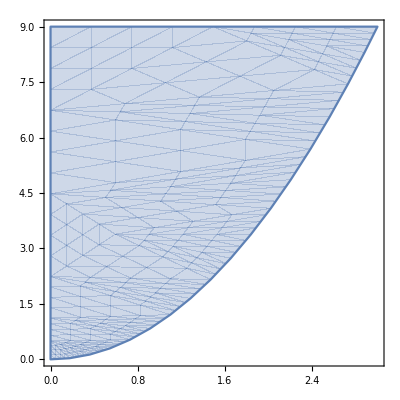

```mathematica
Subscript[r, 1]= ImplicitRegion[y≥x^2 && y≤ 9 && x≥ 0,{x,y}];
RegionPlot[Subscript[r, 1]]
```

```mathematica
(*part 1, a*)
Integrate[x Sqrt[y],{x,0,3},{y,x^2,9}]
```

243/5

```mathematica
(*part 1, b*)
Integrate[x Sqrt[y],{x,y}∈Subscript[r, 1]]
```

243/5

```mathematica
(*part 1, c*)
Integrate[x Sqrt[y],{y,0,9},{x,0,Sqrt[y]}]
```

243/5

```mathematica
(*part 2*)
Plot3D[x Sqrt[y],{y,0,9},{x,0,Sqrt[y]},RegionFunction->(#1 ≥ #2  && #1 ≤ 9 &),Filling->Axis, PlotRange->All, AxesLabel->Automatic]
```

-Graphics3D-

## Problem II: A Triple Integral

Consider the iterated integral, which represents the volume of a region R:

```mathematica
∫_0^1 ∫_(√x)^1 ∫_0^(1-y) 1ⅆzⅆyⅆx
```

1/12

1) Find the volume of the region with a triple integral (not an iterated integral). 

2) We would now like to find the volume or the region using an iterated integral, with order of integration dx dy dz. Do this through the following steps:
	a) Plot the region with RegionPlot3D[ ]. Use the option MeshFunctions -> (#3 &)  to only plot the mesh lines for fixing z (the #3 variable). You probably want to include the options PlotPoints -> 90 to make the edges look better, and AxesLabel -> {x,y,z}.
	
	b) Pick a specific value for z inside the region of integration, and plot the slice in 2D obtained by fixing z at that value. You can use ContourPlot[ ], or RegionPlot[ ]. 
	
	c) Determine the limits of integration for the iterated integral in this order, and use Mathematica to compute the integral.
	
3) Do the same steps as in part (2) just above with the order of integration dz dx dy. You’ll need to adjust your MeshFunctions option, plot the slice at a specific y instead of a specific z.

Note that, by Fubini’s Theorem, you should get the same answer (1/12) when you evaluate all these different integrals.

```mathematica
(*part 1*)
Subscript[r, 2]= ImplicitRegion[z≥0 && z≤ 1-y && y≥ Sqrt[x] && y ≤ 1 && x≥ 0 && x≤ 1,{x,y,z}];
Integrate[1,{x,y,z}∈Subscript[r, 2]]
```

1/12

```mathematica
(*part 2-a*)
RegionPlot3D[z≥0 && z≤ 1-y && y≥ Sqrt[x] && y ≤ 1 && x≥ 0 && x≤ 1,{x,0,1},{y,0,1},{z,0,1},MeshFunctions->(#3 &), PlotPoints->90, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(*part 2-b, region for fixed z*)
Manipulate[RegionPlot[z≤ 1-y && y≥ Sqrt[x] && y ≤ 1 && x≥ 0 ,{x,0,1},{y,0,1}] , {{z, 0.5},0,1}]
```

```mathematica
(*part 2-c*)
Integrate[1,{z,0,1}, {y,0,1-z},{x,0,y^2}]
```

1/12

```mathematica
(*part 3-a*)
RegionPlot3D[z≥0 && z≤  1-y && y≥0 && y ≤ 1 && x≥ 0 && x≤ y^2,{x,0,1},{y,0,1},{z,0,1},MeshFunctions->(#2 &), PlotPoints->90,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(*part 3-b, region for fixed y*)
Manipulate[RegionPlot[z≥0&&z≤ 1-y&&x≥ 0 && x≤ y^2  ,{x,0,1},{z,0,1}] ,{{y, 0.5},0,1}]
```

```mathematica
(*part 3-c*)
Integrate[1,{y,0,1}, {x,0,y^2},{z,0,1-y}]
```

1/12

## Problem III: The Volume of the Unit n-Ball

The unit n-ball (the inside of the unit n-sphere) in ℝ^nis the set of points (x_1,x_2,...,x_n) that satisfy the inequality ∑_(i=1)^n x_i^2≤ 1. For example, for n = 2 this is the unit disc, and for n = 3 this is the unit sphere. Note that for n = 1, the 1-volume (called “length”) is 2, for n = 2, the 2-volume (called “area”) is π, and for n = 3, the 3-volume (just called “volume”) is 4/3 π, so it appears that, at least for small n, the n-volume increases with n.
It is a curious fact that there is a particular dimension n for which the n-dimensional volume of the unit ball is a maximum. 

1) Use Mathematica to find the volume of the unit n-ball by integrating the function f(x_1,x_2,...,x_n) = 1 over the unit n-ball for n = 1, 2, 3, ...,7. 
Note that the last few (n = 5, 6, and 7) are VERY computationally intensive. I suggest you use NIntegrate[ ] to get a (faster) numerical approximation, and make sure your code works before you run it for those n. You may even get some errors if the computer runs out of memory, but it should still give you an answer. 
If you want to see how long the calculations are taking, you can (optionally) put //Timing after your NIntegrate[ ] command and it will tell you how long it took. 

Hints: 
•You can type out all the integrals individually, or you can do this using a Table[ ] to do all of the calculations at once. This may involve the Sum[ ] function. 
•If you use a Table[ ] inside ImplicitRegion[ ], you should wrap it the Table[ ] an Evaluate[ ] command. 
•For n = 1, n = 2 and n = 3, you should get 2, π, and 4/3 π, respectively.
•You can use x[ i ] to get a variable x_i  that you can sum over and use in a table.


2) Use ListPlot[ ] to plot the volumes you got in part (1), and determine which one is the largest.

3) (3 points extra credit) Even though you have now found the n between 1 and 7 for which the volume is maximal, there’s no guarantee that it will continue to decrease for larger n. To verify our maximum is truly a maximum, look online and find a closed formula for the volume of the unit n-ball. Plot this continuous function, combined with your ListPlot[ ] from above, and use Mathematica to find it’s maximum and its limit as n → ∞.

```mathematica
(*part 1*)
Subscript[n, 1]=NIntegrate[1,{x1,-1,1}]
```

2.

```mathematica
Subscript[n, 2]=NIntegrate[1,{x2,-1,1},{x1,-(1-x2^2)^0.5,(1-x2^2)^0.5}]
```

3.14159

```mathematica
Subscript[n, 3]=NIntegrate[1,{x3,-1,1},{x2,-(1-x3^2)^0.5,(1-x3^2)^0.5},{x1,-(1-x3^2-x2^2)^0.5,(1-x3^2-x2^2)^0.5}]
```

4.18879

```mathematica
Subscript[n, 4]=NIntegrate[1,{x4,-1,1},{x3,-(1-x4^2)^0.5,(1-x4^2)^0.5},{x2,-(1-x4^2-x3^2)^0.5,(1-x4^2-x3^2)^0.5},{x1,-(1-x4^2-x3^2-x2^2)^0.5,(1-x4^2-x3^2-x2^2)^0.5}]
```

4.9348

```mathematica
Subscript[n, 5]=NIntegrate[1,{x5,-1,1},{x4,-(1-x5^2)^0.5,(1-x5^2)^0.5},{x3,-(1-x5^2-x4^2)^0.5,(1-x5^2-x4^2)^0.5},{x2,-(1-x5^2-x4^2-x3^2)^0.5,(1-x5^2-x4^2-x3^2)^0.5},{x1,-(1-x5^2-x4^2-x3^2-x2^2)^0.5,(1-x5^2-x4^2-x3^2-x2^2)^0.5}]
```

5.26379

```mathematica
Subscript[n, 6]=NIntegrate[1,{x6,-1,1},{x5,-(1-x6^2)^0.5,(1-x6^2)^0.5},{x4,-(1-x6^2-x5^2)^0.5,(1-x6^2-x5^2)^0.5},{x3,-(1-x6^2-x5^2-x4^2)^0.5,(1-x6^2-x5^2-x4^2)^0.5},{x2,-(1-x6^2-x5^2-x4^2-x3^2)^0.5,(1-x6^2-x5^2-x4^2-x3^2)^0.5},{x1,-(1-x6^2-x5^2-x4^2-x3^2-x2^2)^0.5,(1-x6^2-x5^2-x4^2-x3^2-x2^2)^0.5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5.16771

```mathematica
Subscript[n, 7]=NIntegrate[1,{x7,-1,1},{x6,-(1-x7^2)^0.5,(1-x7^2)^0.5},{x5,-(1-x7^2-x6^2)^0.5,(1-x7^2-x6^2)^0.5},{x4,-(1-x7^2-x6^2-x5^2)^0.5,(1-x7^2-x6^2-x5^2)^0.5},{x3,-(1-x7^2-x6^2-x5^2-x4^2)^0.5,(1-x7^2-x6^2-x5^2-x4^2)^0.5},{x2,-(1-x7^2-x6^2-x5^2-x4^2-x3^2)^0.5,(1-x7^2-x6^2-x5^2-x4^2-x3^2)^0.5},{x1,-(1-x7^2-x6^2-x5^2-x4^2-x3^2-x2^2)^0.5,(1-x7^2-x6^2-x5^2-x4^2-x3^2-x2^2)^0.5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.72477 and 0.0000197568 for the integral and error estimates.

4.72477

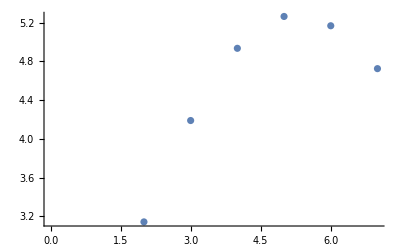

```mathematica
(*part 2*)
ListPlot[{Subscript[n, 1],Subscript[n, 2],Subscript[n, 3],Subscript[n, 4],Subscript[n, 5],Subscript[n, 6],Subscript[n, 7]}]
```

The volume of a 5-dimensional sphere is the largest.

{0}

{5.27777,{n→5.25695}}

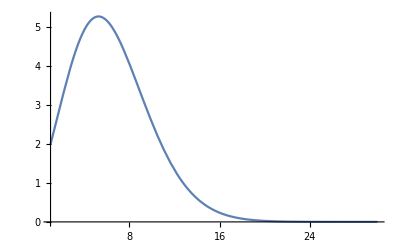

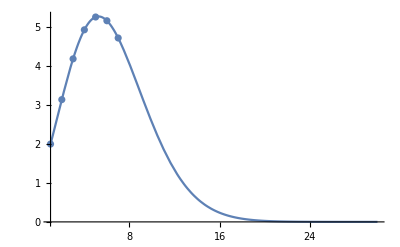

```mathematica
(*extra credit!*)
g[n_] :=(Pi^(n/2))/((n/2)!)
Limit [g[n], {n->Infinity}]
FindMaximum [g[n], n]
Plot[g[n], {n , 1, 30} ]
Show[ 
Plot[g[n],{n , 1,30} ],
ListPlot[{Subscript[n, 1],Subscript[n, 2],Subscript[n, 3],Subscript[n, 4],Subscript[n, 5],Subscript[n, 6],Subscript[n, 7]}]
]
```